# Principal Component Analysis

Principal component analysis (PCA) is a method of dimensionality reduction that is often used in exploratory data science. It allows a high dimensional data set to be projected into a lower number of dimensions while preserving as much variance as possible. In doing so, PCA can easily compress data by expressing the variables in terms of the most important relationship vectors called the principle components. This reduces the dimensions of the dataset, but it results in data loss because the principle components are used to represent the largest amount of variance and therefore can not account for all the variation. PCA has a large variety of applications in data science to reduce the dimensions of large dataset for less computationally challenging manipulations and overall reduce “noisy datasets” in other fields: machine learning, facial recognition, bioinformatics, quantitative finance, and even stock analysis. The main advantage of PCA is its ability to transform a dataset into an dimensionally reduced dataset with independent variables (principle components). This lets users speed up computations and algorithms; it also makes it vary simple to see patterns among the variance of the data (IE. data points will cluster together if they are similar). Disadvantages on the other hand encompass the loss of data and readability. Obviously reducing an object from a given dimension into a lower dimension will result in some sort of loss. Readability ties in with the loss of variables, because everything is expressed in terms of a few principle components a given data point will lose its importance. PCA is ultimately limited by the structure of data it is fed. Datasets with high amounts of linearity and orthogonality will be more accurately expressed in terms of principle components (IE. a 2 dimensional plot resembling the letter “x” would be a perfect candidate for PCA). PCA is also limited by the inherent amount of variation within the dataset. Principle components are attributed with higher variance, a variable with low variance will ultimately result in data loss. In this example we will try to build intuition for how it works by exploring the math visually as we work through a simple example using the covariance method. Then we will apply our generalized understanding to a practical application in an effort to demonstrate how PCA can be useful in the real world.

First, we’ll need a dataset. Here is some science that I did on a couple fruit I found! It’s not very interesting, and to make things worse one of the oranges has a terrible secret (it’s a grapefruit). Even so, this data is perfect for our initial exploration. As we step through the process of projecting our high dimensional data (2) into our lower dimensional space (a number line) we will be able to visualise our actions using tools like ListPlot which would not be applicable to higher dimensional spaces. Take a moment to familiarize yourself with the dataset. (The decision to not use Mathematica’s Dataset function is deliberate, while it may be useful in practice it would impose unnecessary prerequisite knowledge on the readers of this notebook.)

## Dataset

Mass (g) | Height (mm) | Fruit
404 | 89.64 | Orange
446 | 99.81 | Orange
343 | 94.73 | Orange
393 | 99.83 | Orange
383 | 94.22 | Orange
170 | 64.24 | Apple
180 | 72.92 | Apple
186 | 75.58 | Apple
166 | 69.75 | Apple
167 | 69.23 | Apple

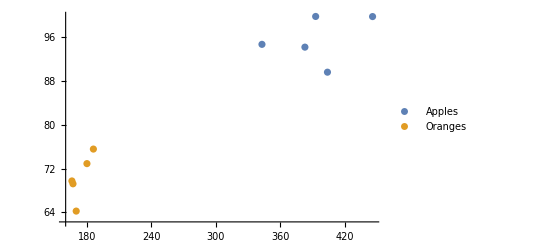

```mathematica
fruits={{404, 89.64, "Orange"}, {446, 99.81, "Orange"}, {343, 94.73, "Orange"}, {393, 99.83, "Orange"}, {383, 94.22, "Orange"}, {170, 64.24, "Apple"}, {180, 72.92, "Apple"}, {186, 75.58, "Apple"}, {166, 69.75, "Apple"}, {167, 69.23, "Apple"}};
TableForm[fruits, TableHeadings->{None, {"Mass (g)", "Height (mm)", "Fruit"}}]
ListPlot[{Select[fruits,#[[3]]=="Orange" &][[All, 1;;2]], Select[fruits,#[[3]]=="Apple" &][[All, 1;;2]]}, PlotLegends->{"Apples", "Oranges"}]
```

Lets drop the labels and create a simple matrix representation of our data.

```mathematica
fruitMat=fruits[[All, 1;;2]];
MatrixForm [fruitMat,TableHeadings-> {None,{"Mass g", "Height mm"}}]
```

(Mass g | Height mm
404 | 89.64
446 | 99.81
343 | 94.73
393 | 99.83
383 | 94.22
170 | 64.24
180 | 72.92
186 | 75.58
166 | 69.75
167 | 69.23)

## Variance

Now that we are familiar with our dataset we can begin to think specifically about the task that we want to accomplish. Our goal is to project our 2 dimensional data onto a single dimension (a line) while preserving as much variation as possible. There are basically two steps in this process. The first is to identify a line in our two dimensional space that points in the direction of highest variance and the second is to project our data-points onto that line. The manipulate below should help you build an intuition for how this process works, take a moment to explore it.

```mathematica
Manipulate[ListPlot[{fruitMat,Table[Projection[fruitMat[[n]]-{x, y}, {Cos[theta], Sin[theta]}]+{x, y}, {n, 1, 10}]}, PlotRange->{{0, 500}, {0, 200}}, PlotStyle->PointSize[0.0175] , Epilog->InfiniteLine[{{x, y},{x+Cos[theta], y+Sin[theta]}}]], {{theta, Pi/4}, 0, Pi}, {{x, 275}, 0, 500}, {{y, 85}, 0, 100}]
```

Notice that the projected data seems to have less variance for theta values around π/2 than it does for theta values around 0. This is  key, our goal is to preserve as much of this variance as possible. In order to maximise it we will need a formal definition of what it actually is. Statistics provides such a definition; variance is an average of the square distance between each data point in one dimension and the mean value of that dimension. In other words, it is a measure of how far the points within a dimension lie from the dimensions mean. We can represent variance with the equation below or compute it using Mathematica’s built in Variance function. The Variance function is the best option in a data science context as it runs in kernel space is is likely much faster and more memory efficient than any thing we could implement in user space, but if you check its documentation you will see that it is functionality identical to the equation below.

S^2=(Σ(x_i-x̄))^2/(n-1)

Lets check the variance of our mass and height dimensions.

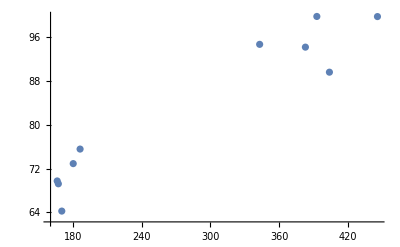

Mass (x) | Height (y)
14092.8 | 194.13

```mathematica
ListPlot[fruitMat]
TableForm[{{fruitMat[[All, 1]]//Variance//N, fruitMat[[All, 2]]//Variance//N}}, TableHeadings->{None, {"Mass (x)", "Height (y)", "Fruit"}}]
```

## Covariance

This is awesome! Our variance values match what we can see in our chart (there is more variance in the x dimension than in the y dimension), but there is one problem. This method only measures variance within a single dimension. For example, it has no way of distinguishing between our list plot above and one where all the heights are negative, we can see below that it will return the same outputs for a dataset that is obviously very different.

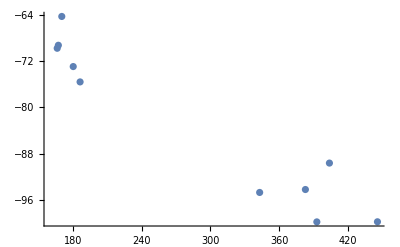

Mass (x) | Height (y)
14092.8 | 194.13

```mathematica
fruitMatNegH=(fruitMat//Transpose)*{1, -1}//Transpose;
ListPlot[fruitMatNegH]
TableForm[{{fruitMatNegH[[All, 1]]//Variance//N, fruitMatNegH[[All, 2]]//Variance//N}}, TableHeadings->{None, {"Mass (x)", "Height (y)", "Fruit"}}]
```

We will need to generalize our concept of variance so that it can be applied to multiple dimensions. In order to do so, we simply replace what would be the second (x_i-x̄) in (x_i-x̄)^2 with (y_i-ȳ) in order to get the equation below. We can see that this equation is identical to the equation for variance if y=x. If y≠x then covariance will measure the extent to which the values in two different dimensions correlate with one another. Mathematica also provides a function for calculating this value called Covariance. Once again, this built in function is likely orders of magnitude more performant than any function we could define from within Mathematica but its functionality is the same as what is written below.

cov_(x,y)=(Σ(x_i-x̄)(y_i-ȳ))/(n-1)

Now if we test our new covariance function on the negative height dataset we defined above we can see how powerful it really is.

```mathematica
ListPlot[fruitMat]
TableForm[{{Covariance[fruitMat[[All, 1]], fruitMat[[All, 1]]]//N, Covariance[fruitMat[[All, 1]], fruitMat[[All, 2]]]//N}, {Covariance[fruitMat[[All, 2]], fruitMat[[All, 1]]]//N, Covariance[fruitMat[[All, 2]], fruitMat[[All, 2]]]//N}}, TableHeadings->{None, {"Mass (x)", "Height (y)", "Fruit"}}]
```

-Graphics-

Mass (x) | Height (y)
14092.8 | 1582.89
1582.89 | 194.13

```mathematica
ListPlot[fruitMatNegH]
TableForm[{{Covariance[fruitMatNegH[[All, 1]], fruitMatNegH[[All, 1]]]//N, Covariance[fruitMatNegH[[All, 2]], fruitMat[[All, 1]]]//N}, {Covariance[fruitMatNegH[[All, 2]], fruitMat[[All, 1]]]//N, Covariance[fruitMatNegH[[All, 2]], fruitMatNegH[[All, 2]]]//N}}, TableHeadings->{None, {"Mass (x)", "Height (y)", "Fruit"}}]
```

-Graphics-

Mass (x) | Height (y)
14092.8 | -1582.89
-1582.89 | 194.13

We can see that our covariance function is capable of returning four separate values for a 2 dimensional data set. Two of these values are simply the variances of each dimension. The other two values represent the covariance of x and y, that is, the extent to which a large value in the x dimension correlates to a large value in the y dimension.

## Covariance Matrix

cov(X)=(cov(x,x) | cov(x, y)
cov(y, x) | cov(x, x))

```mathematica
Covariance[fruitMat]//MatrixForm
```

(14092.8 | 1582.89
1582.89 | 194.13)

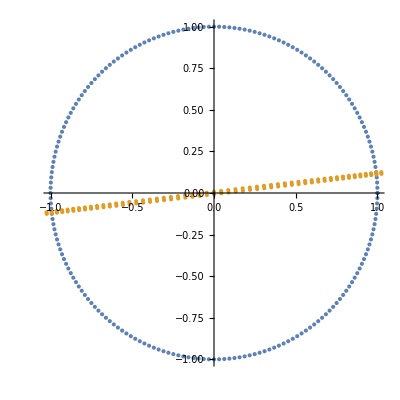

```mathematica
ListPlot[{Table[{Cos[theta], Sin[theta]}, {theta, 0, 2Pi, Pi/100}], Table[{Cos[theta], Sin[theta]}, {theta, 0, 2Pi, Pi/100}].{Normalize[Covariance[fruitMat][[All, 1]]], Normalize[Covariance[fruitMat][[All, 2]]]}}, PlotRange->{{-1, 1}, {-1, 1}}, AspectRatio->1]
```

The Covariance Matrix is linear transformation resulting from the fruit matrix undergoing covariance. Currently the data is in two dimensions.

## Eigenvalues and Eigenvectors

```mathematica
Eigenvalues[Covariance[fruitMat]]
Eigenvectors[Covariance[fruitMat]]
```

{14270.8,16.1374}

{{-0.993737,-0.111743},{0.111743,-0.993737}}

The amount of eigen vectors corresponds to the amount of dimensions. The amount of eigenvalues can be less than or equal the original dimensions of the data.

Notice eigenvectors are orthogonal creating the basis of an orthogonal dimension.

```mathematica
Dot[{-0.9937370885984526,-0.11174345056365227},{0.11174345056365227,-0.9937370885984526}]
```

0.

## Change of Basis

The basis of two eigenvectors is changed into a basis of one eigenvector. This reduces the dimensions into one.

```mathematica
Eigenvectors[Covariance[fruitMat]][[1]]
```

{-0.993737,-0.111743}

## Graphing the Reduced Dimension

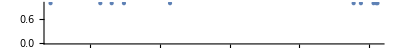

```mathematica
fruitMat.Eigenvectors[Covariance[fruitMat]][[1]]//NumberLinePlot
```

Effectively be selecting one eigenvector from the covariance, the dataset can be represented in terms of one principle component (eigenvector). Ultimately, the two dimensional dataset has been scaled down into one dimension.

## Iris (flower) Dataset

We start by importing the data we want to analyze, the dataset holds 150 entries, but to illustrate the dataset only the first five are shown.

```mathematica
IrisWithLabels=Import["https://archive.ics.uci.edu/ml/machine-learning-databases/iris/iris.data","CSV"][[1;;-2]];
Labeled[TableForm[IrisWithLabels[[{1,2,3,4,5,51,52,53,53,54,101,102,103,104,105}]],TableHeadings->{None,{"Sepal Length","Sepal Width","Petal Length", "Petal Width","Class"}}],"\nFirst Five Entries of Each Type",Top]
```

Sepal Length | Sepal Width | Petal Length | Petal Width | Class
5.1 | 3.5 | 1.4 | 0.2 | Iris-setosa
4.9 | 3. | 1.4 | 0.2 | Iris-setosa
4.7 | 3.2 | 1.3 | 0.2 | Iris-setosa
4.6 | 3.1 | 1.5 | 0.2 | Iris-setosa
5. | 3.6 | 1.4 | 0.2 | Iris-setosa
7. | 3.2 | 4.7 | 1.4 | Iris-versicolor
6.4 | 3.2 | 4.5 | 1.5 | Iris-versicolor
6.9 | 3.1 | 4.9 | 1.5 | Iris-versicolor
6.9 | 3.1 | 4.9 | 1.5 | Iris-versicolor
5.5 | 2.3 | 4. | 1.3 | Iris-versicolor
6.3 | 3.3 | 6. | 2.5 | Iris-virginica
5.8 | 2.7 | 5.1 | 1.9 | Iris-virginica
7.1 | 3. | 5.9 | 2.1 | Iris-virginica
6.3 | 2.9 | 5.6 | 1.8 | Iris-virginica
6.5 | 3. | 5.8 | 2.2 | Iris-virginica
First Five Entries of Each Type

However as you can see this data has the labels of each type of flower attached to it, so in order to perform the Principal Component Analysis we first need to remove the labels.

```mathematica
Iris = IrisWithLabels[[All,1;;4]];
Labeled[TableForm[Iris[[{1,2,3,4,5,51,52,53,53,54,101,102,103,104,105}]],TableHeadings->{None,{"Sepal Length","Sepal Width","Petal Length", "Petal Width"}}],"\nFirst Five Entries of Each Type Without Labels",Top]
```

Sepal Length | Sepal Width | Petal Length | Petal Width
5.1 | 3.5 | 1.4 | 0.2
4.9 | 3. | 1.4 | 0.2
4.7 | 3.2 | 1.3 | 0.2
4.6 | 3.1 | 1.5 | 0.2
5. | 3.6 | 1.4 | 0.2
7. | 3.2 | 4.7 | 1.4
6.4 | 3.2 | 4.5 | 1.5
6.9 | 3.1 | 4.9 | 1.5
6.9 | 3.1 | 4.9 | 1.5
5.5 | 2.3 | 4. | 1.3
6.3 | 3.3 | 6. | 2.5
5.8 | 2.7 | 5.1 | 1.9
7.1 | 3. | 5.9 | 2.1
6.3 | 2.9 | 5.6 | 1.8
6.5 | 3. | 5.8 | 2.2
First Five Entries of Each Type Without Labels

## Fixing the Data

The next important step is calculating the covariance matrix and its eigen values and vectors

```mathematica
covariance = Covariance[Iris ];
Labeled[covariance//MatrixForm,"Covariance Matrix: ",Left]
eigenvectors = Transpose[Eigenvectors[covariance]];
Labeled[eigenvectors//MatrixForm,"Eigen Vectors: \n(As Columns)",Left]
eigenvalues = Eigenvalues[covariance];
Labeled[eigenvalues//MatrixForm,"Eigen Values: ",Left]
```

(0.685694 | -0.0392685 | 1.27368 | 0.516904
-0.0392685 | 0.188004 | -0.321713 | -0.117981
1.27368 | -0.321713 | 3.11318 | 1.29639
0.516904 | -0.117981 | 1.29639 | 0.582414)Covariance Matrix:

(-0.36159 | 0.65654 | -0.580997 | 0.317255
0.0822689 | 0.729712 | 0.596418 | -0.324094
-0.856572 | -0.175767 | 0.0725241 | -0.479719
-0.358844 | -0.0747065 | 0.549061 | 0.751121)Eigen Vectors: 
(As Columns)

(4.22484
0.242244
0.0785239
0.023683)Eigen Values:

Next we calculate the mean vector of the data and subtract it from every entry to center the data at the origin

```mathematica
mean =Mean[Iris];
Labeled[mean//MatrixForm,"Mean Vector: ",Left]
centeredData = Standardize[Iris,Mean,1&];
Labeled[TableForm[centeredData [[50;;60]],TableHeadings->{None,{"Sepal Length","Sepal Width","Petal Length", "Petal Width"}}], "First Ten Entries \nof the Centered Data",Top]
```

(5.84333
3.054
3.75867
1.19867)Mean Vector:

Sepal Length | Sepal Width | Petal Length | Petal Width
-0.843333 | 0.246 | -2.35867 | -0.998667
1.15667 | 0.146 | 0.941333 | 0.201333
0.556667 | 0.146 | 0.741333 | 0.301333
1.05667 | 0.046 | 1.14133 | 0.301333
-0.343333 | -0.754 | 0.241333 | 0.101333
0.656667 | -0.254 | 0.841333 | 0.301333
-0.143333 | -0.254 | 0.741333 | 0.101333
0.456667 | 0.246 | 0.941333 | 0.401333
-0.943333 | -0.654 | -0.458667 | -0.198667
0.756667 | -0.154 | 0.841333 | 0.101333
-0.643333 | -0.354 | 0.141333 | 0.201333First Ten Entries 
of the Centered Data

## Reducing Dimensions

In order to analysis the data in a visual format we want to reduce the number of dimensions down to two. Using PCA we simply choose the two highest eigenvalues of our covariance matrix and using a matrix of their corresponding eigenvectors as our new basis for our data. For this particular example our highest eigenvalues correspond with the first two eigenvectors, so our new basis matrix simply becomes the first two columns of the eigenvector matrix.

```mathematica
PCAbasis = eigenvectors[[All,1;;2]];
Labeled[PCAbasis//MatrixForm,"New Basis",Left]
```

(-0.36159 | 0.65654
0.0822689 | 0.729712
-0.856572 | -0.175767
-0.358844 | -0.0747065)New Basis

Highest PC | Second Highest PC
2.68421 | 0.326607
2.71539 | -0.169557
2.88982 | -0.137346
2.74644 | -0.311124
2.72859 | 0.333925
2.2799 | 0.747783
2.82089 | -0.0821045
2.62648 | 0.170405
2.88796 | -0.570798
2.67384 | -0.106692First Ten Entries 
of the Reduced Data

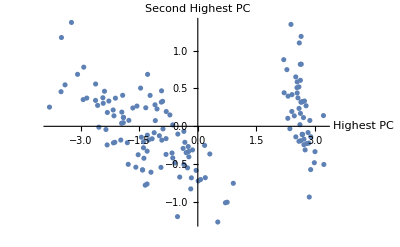
-Graphics-Plot of the Dimensionally Reduced Data

```mathematica
reducedData = Dot[centeredData,PCAbasis];
Labeled[TableForm[reducedData [[1;;10]],TableHeadings->{None,{"Highest PC", "Second Highest PC"}}], "First Ten Entries \nof the Reduced Data",Top]
Labeled[ListPlot[reducedData,AxesLabel->{"Highest PC", "Second Highest PC"}], "Plot of the Dimensionally Reduced Data",Top]
```

## Identifying an Unknown Flower (Application)

To further demonstrate a use case for this, we now make use of the labels attached to each entry. Looking at it we see that each label denotes the type of flower that the entry came from. Let’s say we now had a new data entry without a label.

```mathematica
entry = {5.8,2.8,4.2,1.4};
Labeled[TableForm[{entry},TableHeadings->{None,{"Sepal Length","Sepal Width","Petal Length", "Petal Width","Class"}}],"New Entry",Top]
```

Sepal Length | Sepal Width | Petal Length | Petal Width
5.8 | 2.8 | 4.2 | 1.4New Entry

While it may be do able to compare this entry to just the raw data and estimate the type of flower it came from, the task becomes much easier if we use our dimensionally reduced data  to look for its grouping compared to the other respective flowers.

To start with let’s first take our data plot an color code the points based on which type of flower they came from.

```mathematica
IrisSetosa= reducedData[[1;;50]];
IrisVersicolor = reducedData[[51;;100]];
IrisVirginica = reducedData[[101;;150]];
ListPlot[{IrisSetosa,IrisVersicolor,IrisVirginica},PlotLabels->{"Setosa","Versicolor","Virginica"},AxesLabel->{"Highest PC", "Second Highest PC"}, PlotLabel->"Plot of the Dimensionally Reduced Data"]
```

-Graphics-

Having labeled the points we see that each type falls roughly into three distinct sections, depending on where they lie with respect to our two principal components. The next step to visually estimate which group our new entry belongs to is to transform it into the new basis and plot it on the graph.

```mathematica
centeredEntry = entry-mean;
Labeled[transformedEntry = Dot[centeredEntry,PCAbasis],"Dimensionally Reduced Entry of Unknown Flower Type: ", Left]
Show[ListPlot[{IrisSetosa,IrisVersicolor,IrisVirginica,transformedEntry},PlotLabels->{"Setosa","Versicolor","Virginica"},AxesLabel->{"Highest PC", "Second Highest PC"}, PlotLabel->"Plot of the Dimensionally Reduced Data"],Graphics[{PointSize[Large],Red,Point[transformedEntry]}]]
```

{-0.455508,-0.30641}Dimensionally Reduced Entry of Unknown Flower Type:

-Graphics-

Our new entry seems to fall neatly within the cluster of Versicolor so we can estimate that our data would have been measure from a Versicolor.

In theory this can be used as a method of classifying any new data entry into one of these three flowers based off its relative position in terms of principle components. 

Given any combination of sepal lengths/widths and petal lengths/widths you can categorize an unknown flower into Setosa, Versicolor, and Virginica.

```mathematica
Manipulate[Show[ListPlot[{IrisSetosa,IrisVersicolor,IrisVirginica,transformedEntry},PlotLabels->{"Setosa","Versicolor","Virginica"},AxesLabel->{"Highest PC", "Second Highest PC"}, PlotLabel->"Plot of the Dimensionally Reduced Data"],Graphics[{PointSize[Large],Red,Point[Dot[{a,b,c,d}-mean,PCAbasis]]}]],{{a,5.8,"Sepal Length"},4.3,7.9},{{b,2.8,"Sepal Width"},2,8},{{c,4.2,"Petal Length"},1,6.9},{{d,1.4, "Petal Width"},0.1,2.5}]
```